```mathematica
Needs["ErrorBarPlots`"];
```

The model

```mathematica
ParNames={"y0","x1","σ1","A","x2","σ2"};
Fixed={True,False,False,False,False,False};
StartValue={0,11,0.1,60,14,0.1};
ParMax=Length[ParNames];
UseErr=True;
```

```mathematica
f[x_,y0_,x1_,σ1_,A_,x2_,σ2_]:=y0+A/2*Erf[(x-x1)/(√2 σ1)]+A/2*Erf[-(x-x2)/(√2 σ2)];
```

Create and export dataset with pseudo-random errors for debugging
Compare to fit results of Origin with fit function GaussAmp

Import data
Columns: 1=x, 2=y, 3=yerr

```mathematica
XCol=1;
YCol=10;
YErrCol=11;
```

```mathematica
MyData=Import["D:/Temp/S_parameters_Delay007.tsv","Table"];
```

(* Activate the following to test the use of different columns *)
XCol = 2;
YCol = 3;
YErrCol = 4;
MyData = Transpose[Prepend[Transpose[MyData], Table[Random[], {51}]]]

```mathematica
S3=Part[MyData,All,6];
S3Err=Part[MyData,All,7];
PolarAngle=π/2-ArcCos[S3];
MyData=Transpose[Append[Transpose[MyData],PolarAngle]];
PolarAngleErr=1/(√(1-S3^2))S3Err;
MyData=Transpose[Append[Transpose[MyData],PolarAngleErr]];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
Ind=1;
TheData[Ind]=MyData;
MinTime=Part[First[TheData[Ind]],XCol];
MaxTime=Part[Last[TheData[Ind]],XCol];
MinTime=11;
MaxTime=15;
If[Length[Transpose[TheData[Ind]]]==2||YErrCol==0,UseErr=False;];
```

```mathematica
TheData[Ind]=Select[TheData[Ind],MinTime≤Part[#1,XCol]≤MaxTime&];
```

```mathematica
X[TheTab_]:=Part[TheTab,All,XCol];
Y[TheTab_]:=Part[TheTab,All,YCol];
Err[TheTab_]:=Part[TheTab,All,YErrCol];
DataOnly[TheTab_]:=Part[TheTab,All,{XCol,YCol}];
DataAndErr[TheTab_]:=Table[{{Part[TheTab,Ind,XCol],Part[TheTab,Ind,YCol]},ErrorBar[Part[TheTab,Ind,YErrCol]]},{Ind,Length[TheTab]}];
WeightFunc[x_]:=x^-2;
MyWeights[TheTab_]:=WeightFunc[Part[TheTab,All,YErrCol]];
```

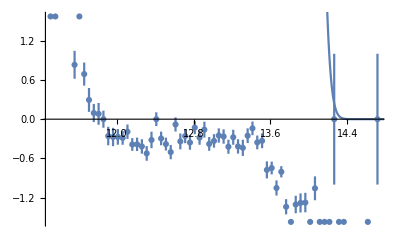

```mathematica
If[UseErr
,(DataPlot=ErrorListPlot[DataAndErr[TheData[Ind]],PlotRange->All]);
,(DataPlot=ListPlot[DataOnly[TheData[Ind]],PlotStyle->PointSize[0.02],PlotRange->All]);]
StartPlot=Plot[Apply[f,Prepend[StartValue,t]],{t,MinTime,MaxTime}];
Show[DataPlot,StartPlot]
```

```mathematica
f[x_]:=If[NumberQ[x],x,"nan"];
SetAttributes[f,Listable];
ExpTab=Part[MyData,All,{1,10,11}];
ExpTab=f[ExpTab];
ExpName="D:/Temp/PolarAngle.txt";
Export[ExpName,SetPrecision[ExpTab,6],"Table"]
```

D:/Temp/PolarAngle.txt